## Geometric parameters

```mathematica
width = 2; height = 1.5;
x1 = 0; x2 =x1 + width;
y1 = 0; y2=y1+height;
ΩΩ=Polygon[{{x1,y1},{x2,y1},{x2,y2},{x1,y2}}];
Γ1=Line[{{x1,y1},{x2,y1}}];(*1. part of boundary*)
Γ2=Line[{{x2,y1},{x2,y2}}];(*2. part of boundary*)
Γ3=Line[{{x2,y2},{x1,y2}}];(*3. part of boundary*)
Γ4=Line[{{x1,y2},{x1,y1}}];(*4. part of boundary*)
Γ=RegionUnion[Γ1,Γ2 ,Γ3,Γ4];(*boundary*)
f[{x_,y_}]:=10;  (*intenzita vonkajsich sil [N/m^2]*)
a[{x_,y_}]:=1; (*tuhost membrany [N/m]*)
nx =7; hx = width/nx;
ny =7; hy=height /ny;

NN =(nx+1)*(ny+1); (*number of points*)
NT=2*nx*ny;(*number of triangles*)

points = Flatten[Table[{X*hx, Y*hy}, {Y,0, ny}, {X, 0, nx}],1];

B=Flatten[Table[{
{Y+(X-1)*(nx+1),Y+1+(X-1)*(nx+1),Y+1+X*(nx+1)}(*Lower triangle*),{Y+(X-1)*(nx+1),Y+1+X*(nx+1),Y+X*(nx+1)}},(*Upper triangle *)
{X,1,nx},{Y,1,ny}],2];

Ω=Table[Triangle[points[[B[[e]]]]],{e,1,NT}];
```

## Visualization

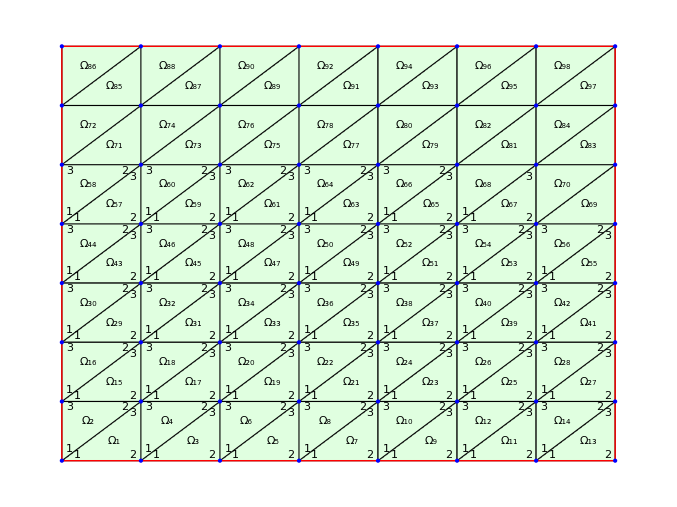

```mathematica
Graphics[{
{FaceForm[LightGreen],EdgeForm[Black],Triangle[Table[points[[B[[i]]]],{i, 1,NT}]],Table[Text[Subscript["Ω",i],Mean[points⟦B⟦i⟧⟧]],{i,1,NT}],Table[Text[Style[ToString[j],Black],Mean[{points[[B[[i,j]]]],Mean[points[[B[[i]]]]]}]+(points[[B[[i,j]]]]-Mean[points[[B[[i]]]]])*0.2],{i,1,NT},{j,1,3}]},(*triangles*)
{Red, Thick,Γ},
{Blue,Point[points],Table[Text[i,points[[i]]+{0.02,0.02}],{i,Length[points]}]} (*points*)
}]
```

## Boundary conditions

```mathematica
g1[{x_,y_}]=Sin[Pi (x-x1)/(x2-x1)]; (*okrajova podmienka na Γ1*)
g2[{x_,y_}]=0.5Sin[3Pi (y-y1)/(y2-y1)]; (*okrajova podmienka na Γ2*)
g3[{x_,y_}]=Sin[Pi (x-x1)/(x2-x1)]x(2-x); (*okrajova podmienka na Γ3*)
g4[{x_,y_}]=Sin[Pi (y-y1)/(y2-y1)]; (*okrajova podmienka na Γ4*)
g1plot=ParametricPlot3D[{x,y1,g1[{x,y1}]},{x,x1,x2},PlotStyle->{Thick,Red},AxesLabel->{Style["x",Large],Style["y",Large],Style["u",Large]}];
g2plot=ParametricPlot3D[{x2,y,g2[{x2,y}]},{y,y1,y2},PlotStyle->{Thick,Red},AxesLabel->{Style["x",Large],Style["y",Large],Style["u",Large]}];
g3plot=ParametricPlot3D[{x,y2,g3[{x,y2}]},{x,x1,x2},PlotStyle->{Thick,Red},AxesLabel->{Style["x",Large],Style["y",Large],Style["u",Large]}];
g4plot=ParametricPlot3D[{x1,y,g4[{x1,y}]},{y,y1,y2},PlotStyle->{Thick,Red},AxesLabel->{Style["x",Large],Style["y",Large],Style["u",Large]}];
gplot=Show[g1plot,g2plot,g3plot,g4plot,PlotRange->All]
```

-Graphics3D-

## Approximate solution

```mathematica
fis= {};
GlobalKe=ConstantArray[0,{NN,NN}];
GlobalFe= ConstantArray[0, NN];
For[e=1, e<=NT,e++, (*iterate triangles*)
(*interpolačné podmienky - riešenie sústavy rovníc cramerovým pravidlom*)
pointsXE=points[[B[[e]],1]];
Xe1=pointsXE[[1]]; Xe2=pointsXE[[2]]; Xe3=pointsXE[[3]]; 
pointsYE=points[[B[[e]],2]];
Ye1=pointsYE[[1]];Ye2=pointsYE[[2]];Ye3=pointsYE[[3]];

ae1=Xe2*Ye3- Xe3*Ye2;
ae2=Xe3*Ye1-Xe1*Ye3;
ae3=Xe1*Ye2-Xe2*Ye1;
det =ae1+ae2+ae3;

be1=Ye2-Ye3;
be2=Ye3-Ye1;
be3=Ye1-Ye2;

ce1=Xe3-Xe2;
ce2 =Xe1-Xe3;
ce3=Xe2-Xe1;

AppendTo[fis, (ae1+be1*x+ce1*y)/det+(ae2+be2*x+ce2*y)/det+(ae3+be3*x+ce3*y)/det];

localKe=Table[Integrate[a[{x,y}]*D[fis[[e,i]],x]*D[fis[[e,j]],x]+D[fis[[e,i]],y]*D[fis[[e,j]],y], Element[{x,y},Ω[[e]]]], {i,3},{j,3}];
localFe=Table[Integrate[f[{x,y}]*fis[[e,i]],Element[{x,y},Ω[[e]]]], {i,3}];

GlobalKe[[B[[e]],B[[e]]]]+=localKe;
GlobalFe[[B[[e]]]]+= localFe;
]
```

## Apply Boundary Conditions - Dirichlet

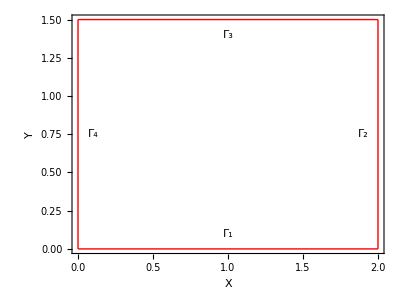

```mathematica
Γplot=Show[RegionPlot[Γ,BoundaryStyle->{Thick,Red},AspectRatio->Automatic],
Graphics[{
Text[Style["\!\(\*SubscriptBox[\(Γ\), \(1\)]\)",Medium],{1,0.1}],(*Bottom boundary*)
Text[Style["\!\(\*SubscriptBox[\(Γ\), \(2\)]\)",Medium],{1.9,0.75}],(*Right boundary*)
Text[Style["\!\(\*SubscriptBox[\(Γ\), \(3\)]\)",Medium],{1,1.4}],(*Top boundary*)
Text[Style["\!\(\*SubscriptBox[\(Γ\), \(4\)]\)",Medium],{0.1,0.75}]  (*Left boundary*)}],
FrameLabel->{Style["X",Large],Style["Y",Large]}]
```

```mathematica
(*Γ1*)
If[g1[{x,y}]===Null,,
xi=0;
For[i=1,i<=nx+1,i++,
GlobalKe[[i]]=IdentityMatrix[NN][[i]];(*vektor, na I tom mieste má 1tku, zvyšok 0*)
GlobalFe[[i]]=g1[{xi,0}];
xi+=hx;
];
];

(*Γ2*)
If[g2[{x,y}]===Null,,
yi=0;
For[i=nx+1,i<=NN,i+=nx+1,
GlobalKe[[i]]=IdentityMatrix[NN][[i]];(*vektor, na I tom mieste má 1tku, zvyšok 0*)
GlobalFe[[i]]=g2[{width,yi}];
yi+=hy;
];
];

(*Γ3*)
If[g3[{x,y}]===Null,,
xi=0;
For[i=NN-nx,i<=NN,i++,
GlobalKe[[i]]=IdentityMatrix[NN][[i]];(*vektor, na I tom mieste má 1tku, zvyšok 0*)
GlobalFe[[i]]=g3[{xi,height}];
xi+=hx;
];
];

(*Γ4*)
If[g4[{x,y}]===Null,,
yi=0;
For[i=1,i<=NN-nx,i+=nx+1,
GlobalKe[[i]]=IdentityMatrix[NN][[i]];(*vektor, na I tom mieste má 1tku, zvyšok 0*)
GlobalFe[[i]]=g4[{0,yi}];
yi+=hy;
];
];
```

## Custom values

```mathematica
z=0; (*bod v poradí*)
value=0.8; (*hodnota bodu*)
If[z==0||z>NN,,
GlobalKe[[z]]=IdentityMatrix[NN][[z]];
GlobalFe[[z]]=value;
]
```

## Solve and Plot

```mathematica
u=LinearSolve[GlobalKe, GlobalFe];
U=Table[{Simplify[Sum[u[[B[[e,i]]]]*fis[[e,i]],{i,3}]], Element[{x,y}, Ω[[e]]]}, {e,1,NT}];
UnGlob=Piecewise[U];
dat=Flatten[Table[Table[{x,y,UnGlob},{x,0,width,hx}],{y,0,height,hy}],1];
solPlot=Graphics3D[{FaceForm[Lighter[Blue]],EdgeForm[Thickness[Medium]],Table[Polygon[dat[[B[[e]]]]],{e,1,NT}]}];
pointPlot=ListPointPlot3D[dat,PlotStyle->{Orange,PointSize[0.025]}];
Show[pointPlot,solPlot]
```

-Graphics3D-

## Real Solution + Approximate Solution

```mathematica
uA[{x_,y_}]=
g1[{x,y1}]Sinh[Pi/(x2-x1)(y2-y)]/Sinh[Pi(y2-y1)/(x2-x1)]+
g2[{x2,y}]Sinh[3Pi/(y2-y1)(x-x1)]/Sinh[3Pi(x2-x1)/(y2-y1)]+
g3[{x,y2}]Sinh[Pi/(x2-x1)(y-y1)]/Sinh[Pi(y2-y1)/(x2-x1)]+
g4[{x1,y}]Sinh[Pi/(y2-y1)(x2-x)]/Sinh[Pi(x2-x1)/(y2-y1)];
uAplot3D=Plot3D[uA[{x,y}],{x,y}∈ΩΩ,AxesLabel->{Style["X",Large],Style["Y",Large],Style["u",Large]},BoxRatios->Automatic,PlotStyle->{Red,Opacity[0.5]},PlotRange->All, Mesh->None];
Show[uAplot3D,solPlot]
```

-Graphics3D-

## EOC

```mathematica
L2Chyba=Sqrt[Sum[NIntegrate[(UnGlob[[1,e,1]]-uA[{x,y}])^2,{x,y}∈Triangle[points[[B[[e]]]]]], {e, NT}]](*sum across all triangles*)
```

1.91034